```mathematica
PERC BNG setup and Carmen's yoke
```

## Load and Initialize Radia

```mathematica
PERC Setup
<<Radia`;|
<< VectorFieldPlots`;

(*Save some Mathematica memory*)
RadUtiMem[];
```

PERC Setup

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

General::obspkg: VectorFieldPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
?rad*
```

## Build the Geometry

```mathematica
RingVolume[Ra_,Ri_,l_,z0_,nnφ_]:=Module[{z,dz,θ,cosθ,φ,dφ,SlicePgn,AllSlicePgns,trapez,AllTrapez},
dz=l;
dφ=2.*π/nnφ;
AllTrapez={};
For[k=0,k≤(nnφ-1),k++,
z=z0-l/2;
AllSlicePgns={};
For[i=1,i≤2,i++,
φ=k dφ;
SlicePgn={};
AppendTo[SlicePgn,{Ri*Cos[φ],Ri*Sin[φ]}];
AppendTo[SlicePgn,{Ra*Cos[φ],Ra*Sin[φ]}];
φ+=dφ;
AppendTo[SlicePgn,{Ra*Cos[φ],Ra*Sin[φ]}];
AppendTo[SlicePgn,{Ri*Cos[φ],Ri*Sin[φ]}];
AllSlicePgns=Append[AllSlicePgns,{SlicePgn,z}];
z+=dz;
];
trapez=radObjMltExtPgn[AllSlicePgns,N[{0,0,0}]];
AppendTo[AllTrapez,trapez];
];
radObjCnt[AllTrapez]
]
```

```mathematica
thcn=0.001;
```

```mathematica
(* coils:  auto-generated from magfield input files *)
Rt1=radObjRaceTrk[{0,0,-7998.21000},{200.583000,210.343000},{0,0},3.58000,12,61.1184,"auto","z"];
radObjDrwAtr[Rt1,{0,1,1},thcn];

Rt2=radObjRaceTrk[{0,0,-3999.99872000},{200.583000,210.343000},{0,0},7992.84256000,12,122.237,"auto","z"];
radObjDrwAtr[Rt2,{0,1,1},thcn];

Rt3=radObjRaceTrk[{0,0,-1.78872000},{200.583000,210.343000},{0,0},3.57744000,12,61.1184,"auto","z"];
radObjDrwAtr[Rt3,{0,1,1},thcn];

Rt4=radObjRaceTrk[{0,0,-132.8000},{207.883000,210.323000},{0,0},80.00,12,-122.237,"auto","z"];
radObjDrwAtr[Rt4,{0,1,1},thcn];

Rt5=radObjRaceTrk[{0,0,-314.4000},{207.883000,210.323000},{0,0},23.000,12,-122.237,"auto","z"];
radObjDrwAtr[Rt5,{0,1,1},thcn];

Rt6=radObjRaceTrk[{0,0,-7998.21000},{210.383000,215.262000},{0,0},3.58000,12,61.1184,"auto","z"];
radObjDrwAtr[Rt6,{0,1,1},thcn];

Rt7=radObjRaceTrk[{0,0,-7928.45000},{210.383000,215.262000},{0,0},135.94000,12,122.237,"auto","z"];
radObjDrwAtr[Rt7,{0,1,1},thcn];

Rt8=radObjRaceTrk[{0,0,-7858.69000},{210.383000,215.262000},{0,0},3.58000,12,61.1184,"auto","z"];
radObjDrwAtr[Rt8,{0,1,1},thcn];

Rt9=radObjRaceTrk[{0,-46.398000,84.7199000},{256.21000,287.02000},{0,0},3.31002589114,12,35.3742,"auto","z"];
radObjDrwAtr[Rt9,{0,1,1},thcn];
radTrfOrnt[Rt9,radTrfRot[{0,-46.398000,84.7199000},{1,0,0},-10.4999241655 Degree]];

Rt10=radObjRaceTrk[{0,-31.000,167.8001000},{256.21000,287.02000},{0,0},165.680128094,12,70.7484,"auto","z"];
radObjDrwAtr[Rt10,{0,1,1},thcn];
radTrfOrnt[Rt10,radTrfRot[{0,-31.000,167.8001000},{1,0,0},-10.4999981687 Degree]];

Rt11=radObjRaceTrk[{0,-15.602000,250.88000},{256.21000,284.65000},{0,0},3.30943593985,12,35.3742,"auto","z"];
radObjDrwAtr[Rt11,{0,1,1},thcn];
radTrfOrnt[Rt11,radTrfRot[{0,-15.602000,250.88000},{1,0,0},-10.5018171622 Degree]];

Rt12=radObjRaceTrk[{0,2.60021000,345.1845000},{314.21000,342.65000},{0,0},3.30936566949,12,35.3742,"auto","z"];
radObjDrwAtr[Rt12,{0,1,1},thcn];
radTrfOrnt[Rt12,radTrfRot[{0,2.60021000,345.1845000},{1,0,0},-21.5043435926 Degree]];

Rt13=radObjRaceTrk[{0,46.999985000,457.9000},{314.21000,345.02000},{0,0},238.980741115,12,70.7484,"auto","z"];
radObjDrwAtr[Rt13,{0,1,1},thcn];
radTrfOrnt[Rt13,radTrfRot[{0,46.999985000,457.9000},{1,0,0},-21.4999214635 Degree]];

Rt14=radObjRaceTrk[{0,91.3998000,570.6155000},{314.21000,345.02000},{0,0},3.30939499607,12,35.3742,"auto","z"];
radObjDrwAtr[Rt14,{0,1,1},thcn];
radTrfOrnt[Rt14,radTrfRot[{0,91.3998000,570.6155000},{1,0,0},-21.5056322247 Degree]];

Rt15=radObjRaceTrk[{0,80.00,741.705000},{300.21000,335.76000},{0,0},3.31000,12,35.3742,"auto","z"];
radObjDrwAtr[Rt15,{0,1,1},thcn];

Rt16=radObjRaceTrk[{0,80.00,1178.7000},{300.21000,335.76000},{0,0},870.68000,12,70.7484,"auto","z"];
radObjDrwAtr[Rt16,{0,1,1},thcn];

Rt17=radObjRaceTrk[{0,80.00,1615.695000},{300.21000,333.39000},{0,0},3.31000,12,35.3742,"auto","z"];
radObjDrwAtr[Rt17,{0,1,1},thcn];

Rt18=radObjRaceTrk[{0,80.00,741.755000},{337.01000,367.82000},{0,0},3.31000,12,35.3742,"auto","z"];
radObjDrwAtr[Rt18,{0,1,1},thcn];

Rt19=radObjRaceTrk[{0,80.00,791.6000},{337.01000,370.19000},{0,0},96.38000,12,70.7484,"auto","z"];
radObjDrwAtr[Rt19,{0,1,1},thcn];

Rt20=radObjRaceTrk[{0,80.00,841.445000},{337.01000,370.19000},{0,0},3.31000,12,35.3742,"auto","z"];
radObjDrwAtr[Rt20,{0,1,1},thcn];

Rt21=radObjRaceTrk[{0,80.00,1516.055000},{337.01000,367.82000},{0,0},3.31000,12,35.3742,"auto","z"];
radObjDrwAtr[Rt21,{0,1,1},thcn];

Rt22=radObjRaceTrk[{0,80.00,1565.9000},{337.01000,370.19000},{0,0},96.38000,12,70.7484,"auto","z"];
radObjDrwAtr[Rt22,{0,1,1},thcn];

Rt23=radObjRaceTrk[{0,80.00,1615.745000},{337.01000,370.19000},{0,0},3.31000,12,35.3742,"auto","z"];
radObjDrwAtr[Rt23,{0,1,1},thcn];

Rt24=radObjRaceTrk[{0,80.00,885.955000},{337.01000,429.44000},{0,0},3.31000,12,37.6687,"auto","z"];
radObjDrwAtr[Rt24,{0,1,1},thcn];

Rt25=radObjRaceTrk[{0,80.00,980.00},{337.01000,429.44000},{0,0},184.78000,12,75.3375,"auto","z"];
radObjDrwAtr[Rt25,{0,1,1},thcn];

Rt26=radObjRaceTrk[{0,80.00,1074.045000},{337.01000,429.44000},{0,0},3.31000,12,37.6687,"auto","z"];
radObjDrwAtr[Rt26,{0,1,1},thcn];

Rt27=radObjRaceTrk[{0,80.00,1283.455000},{337.01000,429.44000},{0,0},3.31000,12,37.6687,"auto","z"];
radObjDrwAtr[Rt27,{0,1,1},thcn];

Rt28=radObjRaceTrk[{0,80.00,1377.5000},{337.01000,429.44000},{0,0},184.78000,12,75.3375,"auto","z"];
radObjDrwAtr[Rt28,{0,1,1},thcn];

Rt29=radObjRaceTrk[{0,80.00,1471.545000},{337.01000,429.44000},{0,0},3.31000,12,37.6687,"auto","z"];
radObjDrwAtr[Rt29,{0,1,1},thcn];

Rt30=radObjRaceTrk[{0,81.99285000,1801.305000},{312.01000,347.56000},{0,0},3.31563322610,12,35.3742,"auto","z"];
radObjDrwAtr[Rt30,{0,1,1},thcn];
radTrfOrnt[Rt30,radTrfRot[{0,81.99285000,1801.305000},{1,0,0},23.9566988991 Degree]];

Rt31=radObjRaceTrk[{0,34.000,1909.1000},{312.01000,347.56000},{0,0},232.676534340,12,70.7484,"auto","z"];
radObjDrwAtr[Rt31,{0,1,1},thcn];
radTrfOrnt[Rt31,radTrfRot[{0,34.000,1909.1000},{1,0,0},24.0003578286 Degree]];

Rt32=radObjRaceTrk[{0,-13.99285000,2016.895000},{312.01000,345.19000},{0,0},3.31563322610,12,35.3742,"auto","z"];
radObjDrwAtr[Rt32,{0,1,1},thcn];
radTrfOrnt[Rt32,radTrfRot[{0,-13.99285000,2016.895000},{1,0,0},23.9566988991 Degree]];

Rt33=radObjRaceTrk[{0,0,2186.04000},{250.582000,270.102000},{0,0},3.58000,12,19.0172,"auto","z"];
radObjDrwAtr[Rt33,{0,1,1},thcn];

Rt34=radObjRaceTrk[{0,0,2682.5000},{250.582000,270.102000},{0,0},989.34000,12,38.0343,"auto","z"];
radObjDrwAtr[Rt34,{0,1,1},thcn];

Rt35=radObjRaceTrk[{0,0,3178.96000},{250.582000,270.102000},{0,0},3.58000,12,19.0172,"auto","z"];
radObjDrwAtr[Rt35,{0,1,1},thcn];

coils={Rt1,Rt2,Rt3,Rt4,Rt5,Rt6,Rt7,Rt8,Rt9,Rt10,Rt11,Rt12,Rt13,Rt14,Rt15,Rt16,Rt17,Rt18,Rt19,Rt20,Rt21,Rt22,Rt23,Rt24,Rt25,Rt26,Rt27,Rt28,Rt29,Rt30,Rt31,Rt32,Rt33,Rt34,Rt35};
Grp=radObjCnt[coils];
```

#### Shielding

```mathematica
(*copy of coils*)
Rt1c=radObjRaceTrk[{0,0,-4000},{200.0,207.9000},{0,0},8000,12,150.976,"auto","z"];
radObjDrwAtr[Rt1c,{0,1,1},thcn];

Rt2c=radObjRaceTrk[{0,0,-123.3000},{205.9000,207.9000},{0,0},78.8000,12,-149.095,"auto","z"];
radObjDrwAtr[Rt2c,{0,1,1},thcn];

Rt3c=radObjRaceTrk[{0,0,-306.3000},{205.9000,207.9000},{0,0},22.9000,12,-148.952,"auto","z"];
radObjDrwAtr[Rt3c,{0,1,1},thcn];

Rt4c=radObjRaceTrk[{0,0,-7926.26000},{207.9000,211.9000},{0,0},147.48000,12,149.041,"auto","z"];
radObjDrwAtr[Rt4c,{0,1,1},thcn];

Rt5c=radObjRaceTrk[{0,-31.000,167.79985000},{260.00,289.58000},{0,0},172.307975839,12,73.9129,"auto","z"];
radObjDrwAtr[Rt5c,{0,1,1},thcn];
radTrfOrnt[Rt5c,radTrfRot[{0,-31.000,167.79985000},{1,0,0},-10.4970123332 Degree]];

Rt6c=radObjRaceTrk[{0,47.039845000,457.9000},{315.000,344.5000},{0,0},245.677034850,12,73.8731,"auto","z"];
radObjDrwAtr[Rt6c,{0,1,1},thcn];
radTrfOrnt[Rt6c,radTrfRot[{0,47.039845000,457.9000},{1,0,0},-21.4657580774 Degree]];

Rt7c=radObjRaceTrk[{0,80.00,1178.7000},{300.0,334.1000},{0,0},877.3000,12,73.797,"auto","z"];
radObjDrwAtr[Rt7c,{0,1,1},thcn];

Rt8c=radObjRaceTrk[{0,80.00,794.3000},{335.1000,362.37000},{0,0},108.5000,12,73.8008,"auto","z"];
radObjDrwAtr[Rt8c,{0,1,1},thcn];

Rt9c=radObjRaceTrk[{0,80.00,1563.1000},{335.1000,362.37000},{0,0},108.5000,12,73.8008,"auto","z"];
radObjDrwAtr[Rt9c,{0,1,1},thcn];

Rt10c=radObjRaceTrk[{0,80.00,981.2000},{335.1000,423.78000},{0,0},191.4000,12,1.2,"auto","z"];
radObjDrwAtr[Rt10c,{0,1,1},thcn];

Rt11c=radObjRaceTrk[{0,80.00,1376.2000},{335.1000,423.78000},{0,0},191.4000,12,1.2,"auto","z"];
radObjDrwAtr[Rt11c,{0,1,1},thcn];

Rt12c=radObjRaceTrk[{0,34.000,1909.1000},{311.8000,345.9000},{0,0},239.299583826,12,73.7865,"auto","z"];
radObjDrwAtr[Rt12c,{0,1,1},thcn];
radTrfOrnt[Rt12c,radTrfRot[{0,34.000,1909.1000},{1,0,0},23.9947296305 Degree]];

Rt13c=radObjRaceTrk[{0,0,2682.5000},{250.00,261.8000},{0,0},996.5000,12,76.6085,"auto","z"];
radObjDrwAtr[Rt13c,{0,1,1},thcn];
 
coilsc={Rt1c,Rt2c,Rt3c,Rt4c,Rt5c,Rt6c,Rt7c,Rt8c,Rt9c,Rt10c,Rt11c,Rt12c,Rt13c};
```

```mathematica
(*Ersatz für Permanentmagnete-> "guiding field"*)

(*Rt14=radObjRaceTrk[{70,0,-8490},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rt14,{0,0.2,1},thcn];
Rt14drw = radObjDrw[Rt14];

Rt15=radObjRaceTrk[{-70,0,-8490},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rt15,{0,0.6,0.6},thcn];
Rt15drw = radObjDrw[Rt15];*)

(*gekippte Spulen*)
Rtg16=radObjRaceTrk[{70,0,-8590},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg16,{0,0.2,1},thcn];
radTrfOrnt[Rtg16,radTrfRot[{70,0,-8590},{1,0,0},-10.0Degree]];
Rtg16drw = radObjDrw[Rtg16];

Rtg17=radObjRaceTrk[{-70,0,-8590},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg17,{0,0.6,0.6},thcn];
radTrfOrnt[Rtg17,radTrfRot[{-70,0,-8590},{1,0,0},-10.0Degree]];
Rtg17drw = radObjDrw[Rtg17];

Rtg18=radObjRaceTrk[{70,0,-8670},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg18,{0,1,1},thcn];
Rtg18drw = radObjDrw[Rtg18];

Rtg19=radObjRaceTrk[{-70,0,-8670},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg19,{0,1,1},thcn];
Rtg19drw = radObjDrw[Rtg19];


Rtg22=radObjRaceTrk[{70,0,-8750},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg22,{0,1,1},thcn];
Rtg22drw = radObjDrw[Rtg22];

Rtg23=radObjRaceTrk[{-70,0,-8750},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg23,{0.5,0,0.5},thcn];
Rtg23drw = radObjDrw[Rtg23];


Rtg26=radObjRaceTrk[{70,0,-8830},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg26,{0,0.8,0.5},thcn];
Rtg26drw = radObjDrw[Rtg26];

Rtg27=radObjRaceTrk[{-70,0,-8830},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg27,{0,0.8,0.5},thcn];
Rtg27drw = radObjDrw[Rtg27];

Rtg28=radObjRaceTrk[{70,0,-8910},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg28,{0,0.8,0.5},thcn];
Rtg28drw = radObjDrw[Rtg28];

Rtg29=radObjRaceTrk[{-70,0,-8910},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg29,{0,0.8,0.5},thcn];
Rtg29drw = radObjDrw[Rtg29];

Rtg30=radObjRaceTrk[{70,0,-8990},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg30,{0,0.8,0.5},thcn];
Rtg30drw = radObjDrw[Rtg30];

Rtg31=radObjRaceTrk[{-70,0,-8990},{6,12},{0,0},180,12,75,"auto","y"];
radObjDrwAtr[Rtg31,{0,0.8,0.5},thcn];
Rtg31drw = radObjDrw[Rtg31];
```

{0.,0.00002035,0.0000266413,0.0000337439,0.0000418035,0.0000513496,0.0000605714,0.0000703292,0.0000817075,0.0000931149,0.000103244,0.000111338,0.000123719,0.000138442,0.000158027,0.000206113,0.000304661,0.000423259,0.000578011,0.000879719,0.00124451,0.00180436}

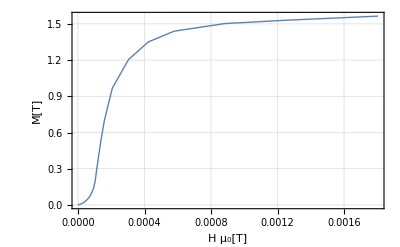

```mathematica
(*Material assignment to shielding according to permeability plots from "murB2_Armcopos.txt" *)
f=Import["/home/matteo/Downloads/murB2_Armcopos.txt","table"];
H=f[[All,1]]/f[[All,2]]
M=(f[[All,2]]-1)*H;
ListPlot[{Transpose[{H,M}]},Frame->True,Axes->False,FrameLabel->{"H µ_0[T] ","M[T]"},LabelStyle->{18},Joined->True,PlotStyle->Thick]
```

```mathematica
(*Abschirmung*)

(*Vorderer Rahmen*)

r1v= radObjRecMag[{0,1150,-8380},{2800,140,140},{0,0,0}];
radObjDrwAtr[r1v,{0,1,1},thcn];
radObjDivMag[r1v,{{100,1},{140,1},{140,1}},kxkykz->Size];
r1vdrw = radObjDrw[r1v];

r2v= radObjRecMag[{0,-1150,-8380},{2800,140,140},{0,0,0}];
radObjDrwAtr[r2v,{0,1,1},thcn];
radObjDivMag[r2v,{{100,1},{140,1},{140,1}},kxkykz->Size];
r2vdrw = radObjDrw[r2v];

r3v= radObjRecMag[{1500,0,-8380},{140,2100,140},{0,0,0}];
radObjDrwAtr[r3v,{0,1,1},thcn];
radObjDivMag[r3v,{{140,1},{100,1},{140,1}},kxkykz->Size];
r3vdrw = radObjDrw[r3v];

r4v= radObjRecMag[{-1500,0,-8380},{140,2100,140},{0,0,0}];
radObjDrwAtr[r4v,{0,1,1},thcn];
radObjDivMag[r4v,{{140,1},{100,1},{140,1}},kxkykz->Size];
r4vdrw = radObjDrw[r4v];


(*zusätzliche Querstreben vorne*)

r5v= radObjRecMag[{785,0,-8380},{1290,140,140},{0,0,0}];
radObjDrwAtr[r5v,{0,1,1},thcn];
radObjDivMag[r5v,{{40,1},{20,1},{20,1}},kxkykz->Size];
r5vdrw = radObjDrw[r5v];

r6v= radObjRecMag[{-785,0,-8380},{1290,140,140},{0,0,0}];
radObjDrwAtr[r6v,{0,1,1},thcn];
radObjDivMag[r6v,{{40,1},{20,1},{20,1}},kxkykz->Size];
r6vdrw = radObjDrw[r6v];



(*Detektorfläche*)
prisma1= radObjThckPgn[0,140,{{-8450,-60},{-8450,-140},{-8310,-140}},"y"];
radObjDivMag[prisma1,{{7,1},{2,1},{7,1}},{"cyl",{{-140,0,-8310},{0,140,0}},{-60,0,-8450},1},kxkykz->Numb,Frame->Lab];
radObjDrwAtr[prisma1,{0,1,1},thcn];
prisma1drw = radObjDrw[prisma1];

prisma2 = radObjThckPgn[0,140,{{-8450,60},{-8450,140},{-8310,140}(*,{-8370,50}*)},"y"];
radObjDivMag[prisma2,{{7,1},{2,1},{7,1}},{"cyl",{{140,0,-8310},{0,140,0}},{60,0,-8450},1},kxkykz->Numb,Frame->Lab];
radObjDrwAtr[prisma2,{0,1,1},thcn];
prisma2drw = radObjDrw[prisma2];


(* hinterer Rahmen*)

r1h= radObjRecMag[{0,1150,3950},{2800,200,200},{0,0,0}];
radObjDrwAtr[r1h,{0,1,1},thcn];
radObjDivMag[r1h,{{100,1},{100,1},{100,1}},kxkykz->Size];


r2h= radObjRecMag[{0,-1150,3950},{2800,200,200},{0,0,0}];
radObjDrwAtr[r2h,{0,1,1},thcn];
radObjDivMag[r2h,{{100,1},{100,1},{100,1}},kxkykz->Size];


r3h= radObjRecMag[{1500,0,3950},{200,2100,200},{0,0,0}];
radObjDrwAtr[r3h,{0,1,1},thcn];
radObjDivMag[r3h,{{100,1},{100,1},{100,1}},kxkykz->Size];


r4h= radObjRecMag[{-1500,0,3950},{200,2100,200},{0,0,0}];
radObjDrwAtr[r4h,{0,1,1},thcn];
radObjDivMag[r4h,{{100,1},{100,1},{100,1}},kxkykz->Size];

(* vordere Abschirmplatten*)

p1v= radObjRecMag[{1375,0,-7160},{50,2500,2300},{0,0,0}];
radObjDrwAtr[p1v,{0,1,1},thcn];
radObjDivMag[p1v,{{50,1},{100,1},{100,1}},kxkykz->Size];

p2v= radObjRecMag[{-1375,0,-7160},{50,2500,2300},{0,0,0}];
radObjDrwAtr[p2v,{0,1,1},thcn];
radObjDivMag[p2v,{{50,1},{100,1},{100,1}},kxkykz->Size];


(* Balken*)

b1= radObjRecMag[{1500,1150,-2200},{200,200,12100},{0,0,0}];
radObjDrwAtr[b1,{0,1,1},thcn];
radObjDivMag[b1,{{100,1},{100,1},{100,1}},kxkykz->Size];

b2= radObjRecMag[{-1500,1150,-2200},{200,200,12100},{0,0,0}];
radObjDrwAtr[b2,{0,1,1},thcn];
radObjDivMag[b2,{{100,1},{100,1},{100,1}},kxkykz->Size];

b3= radObjRecMag[{1500,-1150,-2200},{200,200,12100},{0,0,0}];
radObjDrwAtr[b3,{0,1,1},thcn];
radObjDivMag[b3,{{100,1},{100,1},{100,1}},kxkykz->Size];

b4= radObjRecMag[{-1500,-1150,-2200},{200,200,12100},{0,0,0}];
radObjDrwAtr[b4,{0,1,1},thcn];
radObjDivMag[b4,{{100,1},{100,1},{100,1}},kxkykz->Size];


(*hintere Abschirmplatten*)

p1hi= radObjRecMag[{1125,0,1150},{50,2500,2300},{0,0,0}];
radObjDrwAtr[p1hi,{0,1,1},thcn];
radObjDivMag[p1hi,{{25,1},{250,1},{100,1}},kxkykz->Size];

p2hi= radObjRecMag[{-1125,0,1150},{50,2500,2300},{0,0,0}];
radObjDrwAtr[p2hi,{0,1,1},thcn];
radObjDivMag[p2hi,{{25,1},{250,1},{100,1}},kxkykz->Size];

p1hm= radObjRecMag[{1225,0,-100},{50,2500,2500},{0,0,0}];
radObjDrwAtr[p1hm,{0,1,1},thcn];
radObjDivMag[p1hm,{{25,1},{250,1},{100,1}},kxkykz->Size];
 
p2hm= radObjRecMag[{-1225,0,-100},{50,2500,2500},{0,0,0}];
radObjDrwAtr[p2hm,{0,1,1},thcn];
radObjDivMag[p2hm,{{25,1},{250,1},{100,1}},kxkykz->Size];

p1hm2= radObjRecMag[{1225,0,1775},{50,2500,1250},{0,0,0}];
radObjDrwAtr[p1hm2,{0,1,1},thcn];
radObjDivMag[p1hm2,{{25,1},{250,1},{50,1}},kxkykz->Size];
 
p2hm2= radObjRecMag[{-1225,0,1775},{50,2500,1250},{0,0,0}];
radObjDrwAtr[p2hm2,{0,1,1},thcn];
radObjDivMag[p2hm2,{{25,1},{250,1},{50,1}},kxkykz->Size];

p1hm3= radObjRecMag[{1225,0,3025},{50,2500,1250},{0,0,0}];
radObjDrwAtr[p1hm3,{0,1,1},thcn];
radObjDivMag[p1hm3,{{25,1},{250,1},{50,1}},kxkykz->Size];
 
p2hm3= radObjRecMag[{-1225,0,3025},{50,2500,1250},{0,0,0}];
radObjDrwAtr[p2hm3,{0,1,1},thcn];
radObjDivMag[p2hm3,{{25,1},{250,1},{50,1}},kxkykz->Size];

p1ha= radObjRecMag[{1325,0,-100},{50,2500,2500},{0,0,0}];
radObjDrwAtr[p1ha,{0,1,1},thcn];
radObjDivMag[p1ha,{{25,1},{250,1},{100,1}},kxkykz->Size];

p2ha= radObjRecMag[{-1325,0,-100},{50,2500,2500},{0,0,0}];
radObjDrwAtr[p2ha,{0,1,1},thcn];
radObjDivMag[p2ha,{{25,1},{250,1},{100,1}},kxkykz->Size]; 

p1ha2= radObjRecMag[{1325,0,1775},{50,2500,1250},{0,0,0}];
radObjDrwAtr[p1ha2,{0,1,1},thcn];
radObjDivMag[p1ha2,{{25,1},{250,1},{50,1}},kxkykz->Size];

p2ha2= radObjRecMag[{-1325,0,1775},{50,2500,1250},{0,0,0}];
radObjDrwAtr[p2ha2,{0,1,1},thcn];
radObjDivMag[p2ha2,{{25,1},{250,1},{50,1}},kxkykz->Size]; 

p1ha3= radObjRecMag[{1325,0,3025},{50,2500,1250},{0,0,0}];
radObjDrwAtr[p1ha3,{0,1,1},thcn];
radObjDivMag[p1ha3,{{25,1},{250,1},{50,1}},kxkykz->Size];

p2ha3= radObjRecMag[{-1325,0,3025},{50,2500,1250},{0,0,0}];
radObjDrwAtr[p2ha3,{0,1,1},thcn];
radObjDivMag[p2ha3,{{25,1},{250,1},{50,1}},kxkykz->Size]; 



(*vorne:obere rechte Ecke*)

p11=radObjPolyhdr[{{-1400,1050,-8450},{-1600,1050,-8450},{-1600,1250,-8450},{-1400,1250,-8450},{-1400,1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p11,{2,2,2},{"cyl",{{-1400,1050,-8450},{0,0,50}},{-1550,1200,0},1},Frame-> Lab];
radObjDrwAtr[p11,{0,1,1},thcn];
p11drw = radObjDrw[p11];

p12=radObjPolyhdr[{{-1400,1250,-8250},{-1400,1250,-8450},{-1600,1250,-8450},{-1600,1250,-8250},{-1400,1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p12,{2,2,2},{"cyl",{{-1400,1250,-8250},{0,50,0}},{-1550,0,-8400},1},Frame-> Lab];
radObjDrwAtr[p12,{0,1,1},thcn];
p12drw = radObjDrw[p12];


p13=radObjPolyhdr[{{-1600,1050,-8450},{-1600,1050,-8250},{-1600,1250,-8250},{-1600,1250,-8450},{-1400,1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p13,{2,2,2},{"cyl",{{-1600,1050,-8250},{50,0,0}},{0,1200,-8400},1},Frame-> Lab];
radObjDrwAtr[p13,{0,1,1},thcn];
p13drw = radObjDrw[p13];
(*Show[Graphics3D[{p11drw,p12drw,p13drw}],PlotLabel->"Test",BaseStyle -> {14, FontFamily -> "Times"},PlotRange -> All,Axes -> True]*)


(*vorne:untere rechte Ecke*)

p21=radObjPolyhdr[{{-1400,-1250,-8450},{-1600,-1250,-8450},{-1600,-1050,-8450},{-1400,-1050,-8450},{-1400,-1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p21,{2,2,2},{"cyl",{{-1400,-1050,-8450},{0,0,50}},{-1550,-1200,0},1},Frame-> Lab];
radObjDrwAtr[p21,{0,1,1},thcn];
p21drw = radObjDrw[p21];

p22=radObjPolyhdr[{{-1600,-1250,-8450},{-1600,-1250,-8250},{-1600,-1050,-8250},{-1600,-1050,-8450},{-1400,-1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p22,{2,2,2},{"cyl",{{-1600,-1050,-8250},{50,0,0}},{0,-1200,-8400},1},Frame-> Lab];
radObjDrwAtr[p22,{0,1,1},thcn];
p22drw = radObjDrw[p22];

p23=radObjPolyhdr[{{-1400,-1250,-8250},{-1600,-1250,-8250},{-1600,-1250,-8450},{-1400,-1250,-8450},{-1400,-1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p23,{2,2,2},{"cyl",{{-1400,-1250,-8250},{0,50,0}},{-1550,0,-8400},1},Frame-> Lab];
radObjDrwAtr[p23,{0,1,1},thcn];
p23drw = radObjDrw[p23];
(*Show[Graphics3D[{p21drw,p22drw}],PlotLabel->"Test",BaseStyle -> {14, FontFamily -> "Times"},PlotRange -> All,Axes -> True]*)


(*vorne: untere linke Ecke*)

p31=radObjPolyhdr[{{1600,-1250,-8450},{1400,-1250,-8450},{1400,-1050,-8450},{1600,-1050,-8450},{1400,-1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p31,{2,2,2},{"cyl",{{1400,-1050,-8450},{0,0,50}},{1550,-1200,0},1},Frame-> Lab];
radObjDrwAtr[p31,{0,1,1},thcn];
p31drw = radObjDrw[p31];

p32=radObjPolyhdr[{{1600,-1250,-8250},{1400,-1250,-8250},{1400,-1250,-8450},{1600,-1250,-8450},{1400,-1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p32,{2,2,2},{"cyl",{{1400,-1250,-8250},{0,50,0}},{1550,0,-8400},1},Frame-> Lab];
radObjDrwAtr[p32{0,1,1},thcn];
p32drw = radObjDrw[p32];

p33=radObjPolyhdr[{{1600,-1250,-8450},{1600,-1050,-8450},{1600,-1050,-8250},{1600,-1250,-8250},{1400,-1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p33,{2,2,2},{"cyl",{{1600,-1050,-8250},{50,0,0}},{0,-1200,-8400},1},Frame-> Lab];
radObjDrwAtr[p33,{0,1,1},thcn];
p33drw = radObjDrw[p33];
(*Show[Graphics3D[{p31drw}],PlotLabel->"Test",BaseStyle -> {14, FontFamily -> "Times"},PlotRange -> All,Axes -> True]*)


(*vorne: obere linke Ecke*)
p41=radObjPolyhdr[{{1600,1050,-8450},{1400,1050,-8450},{1400,1250,-8450},{1600,1250,-8450},{1400,1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p41,{2,2,2},{"cyl",{{1400,1050,-8450},{0,0,50}},{1550,1200,0},1},Frame-> Lab];
radObjDrwAtr[p41,{0,1,1},thcn];
p41drw = radObjDrw[p41];

p42=radObjPolyhdr[{{1600,1250,-8450},{1400,1250,-8450},{1400,1250,-8250},{1600,1250,-8250},{1400,1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p42,{2,2,2},{"cyl",{{1400,1250,-8250},{0,50,0}},{1550,0,-8400},1},Frame-> Lab];
radObjDrwAtr[p42,{0,1,1},thcn];
p42drw = radObjDrw[p42];


p43=radObjPolyhdr[{{1600,1250,-8250},{1600,1050,-8250},{1600,1050,-8450},{1600,1250,-8450},{1400,1050,-8250}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p43,{2,2,2},{"cyl",{{1600,1050,-8250},{50,0,0}},{0,1200,-8400},1},Frame-> Lab];
radObjDrwAtr[p43,{0,1,1},thcn];
p43drw = radObjDrw[p43];
(*Show[Graphics3D[{p41drw,p42drw,p43drw}],PlotLabel->"Test",BaseStyle -> {14, FontFamily -> "Times"},PlotRange -> All,Axes -> True]*)

(*hinten: obere linke Ecke*)

p51=radObjPolyhdr[{{-1600,1050,4050},{-1400,1050,4050},{-1400,1250,4050},{-1600,1250,4050},{-1400,1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p51,{2,2,2},{"cyl",{{-1400,1050,4050},{0,0,50}},{-1550,1200,0},1},Frame-> Lab];
p51drw = radObjDrw[p51];

p52=radObjPolyhdr[{{-1600,1250,4050},{-1400,1250,4050},{-1400,1250,3850},{-1600,1250,3850},{-1400,1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p52,{2,2,2},{"cyl",{{-1400,1250,3850},{0,50,0}},{-1550,0,4000},1},Frame-> Lab];
p52drw = radObjDrw[p52];

-Graphics3D-
p53=radObjPolyhdr[{{-1600,1250,3850},{-1600,1050,3850},{-1600,1050,4050},{-1600,1250,4050},{-1400,1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p53,{2,2,2},{"cyl",{{-1600,1050,3850},{50,0,0}},{0,1200,4000},1},Frame-> Lab];
p53drw = radObjDrw[p53];
(*Show[Graphics3D[{p51drw,p52drw,p53drw}],PlotLabel->"Test",BaseStyle -> {14, FontFamily -> "Times"},PlotRange -> All,Axes -> True]*)

(*hinten:obere rechte Ecke*)

p61=radObjPolyhdr[{{1400,1050,4050},{1600,1050,4050},{1600,1250,4050},{1400,1250,4050},{1400,1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p61,{2,2,2},{"cyl",{{1400,1050,4050},{0,0,50}},{1550,1200,0},1},Frame-> Lab];
p61drw = radObjDrw[p61];

p62=radObjPolyhdr[{{1400,1250,3850},{1400,1250,4050},{1600,1250,4050},{1600,1250,3850},{1400,1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p62,{2,2,2},{"cyl",{{1400,1250,3850},{0,50,0}},{1550,0,4000},1},Frame-> Lab];
p62drw = radObjDrw[p62];


p63=radObjPolyhdr[{{1600,1050,4050},{1600,1050,3850},{1600,1250,3850},{1600,1250,4050},{1400,1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p63,{2,2,2},{"cyl",{{1600,1050,3850},{50,0,0}},{0,1200,4000},1},Frame-> Lab];
p63drw = radObjDrw[p63];
(*Show[Graphics3D[{p61drw,p62drw,p63drw}],PlotLabel->"Test",BaseStyle -> {14, FontFamily -> "Times"},PlotRange -> All,Axes -> True]*)


(*hinten:untere rechte Ecke*)

p71=radObjPolyhdr[{{1400,-1250,4050},{1600,-1250,4050},{1600,-1050,4050},{1400,-1050,4050},{1400,-1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p71,{2,2,2},{"cyl",{{1400,-1050,4050},{0,0,50}},{1550,-1200,0},1},Frame-> Lab];
p71drw = radObjDrw[p71];

p72=radObjPolyhdr[{{1600,-1250,4050},{1600,-1250,3850},{1600,-1050,3850},{1600,-1050,4050},{1400,-1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p72,{2,2,2},{"cyl",{{1600,-1050,3850},{50,0,0}},{0,-1200,4000},1},Frame-> Lab];
p72drw = radObjDrw[p72];

p73=radObjPolyhdr[{{1400,-1250,3850},{1600,-1250,3850},{1600,-1250,4050},{1400,-1250,4050},{1400,-1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p73,{2,2,2},{"cyl",{{1400,-1250,3850},{0,50,0}},{1550,0,4000},1},Frame-> Lab];
p73drw = radObjDrw[p73];
(*Show[Graphics3D[{p71drw,p72drw,p73drw}],PlotLabel->"Test",BaseStyle -> {14, FontFamily -> "Times"},PlotRange -> All,Axes -> True]*)

(*hinten: untere linke Ecke*)

p81=radObjPolyhdr[{{-1600,-1250,4050},{-1400,-1250,4050},{-1400,-1050,4050},{-1600,-1050,4050},{-1400,-1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p81,{2,2,2},{"cyl",{{-1400,-1050,4050},{0,0,50}},{-1550,-1200,0},1},Frame-> Lab];
p81drw = radObjDrw[p81];

p82=radObjPolyhdr[{{-1600,-1250,3850},{-1400,-1250,3850},{-1400,-1250,4050},{-1600,-1250,4050},{-1400,-1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p82,{2,2,2},{"cyl",{{-1400,-1250,3850},{0,50,0}},{-1550,0,4000},1},Frame-> Lab];
p82drw = radObjDrw[p82];

p83=radObjPolyhdr[{{-1600,-1250,4050},{-1600,-1050,4050},{-1600,-1050,3850},{-1600,-1250,3850},{-1400,-1050,3850}},{{1,2,3,4},{1,2,5},{2,3,5},{3,4,5},{1,4,5}},{0,0,0}];
radObjDivMag[p83,{2,2,2},{"cyl",{{-1600,-1050,3850},{50,0,0}},{0,-1200,4000},1},Frame-> Lab];
p83drw = radObjDrw[p83];
(*Show[Graphics3D[{p81drw,p82drw,p83drw}],PlotLabel->"Test",BaseStyle -> {14, FontFamily -> "Times"},PlotRange -> All,Axes -> True]*)
```

-Graphics3D-

```mathematica
(*Permanentmagnet*)

steelplate1= radObjRecMag[{0,-95,-9000},{160,10,1000},{0,0,0}];
radObjDrwAtr[steelplate1,{0,1,1},thcn];
radObjDivMag[steelplate1,{{20,1},{10,1},{10,1}},kxkykz->Size];
stpl1drw = radObjDrw[steelplate1];

steelplate2= radObjRecMag[{0,95,-9000},{160,10,1000},{0,0,0}];
radObjDrwAtr[steelplate2,{0,1,1},thcn];
radObjDivMag[steelplate2,{{20,1},{10,1},{10,1}},kxkykz->Size];
stpl2drw = radObjDrw[steelplate2];

(*steelplate3= radObjRecMag[{0,-95,-8550},{200,10,100},{0,0,0}];
radObjDrwAtr[steelplate3,{0,1,1},thcn];
radObjDivMag[steelplate3,{{20,1},{10,1},{20,1}},kxkykz->Size];
radTrfOrnt[steelplate3,radTrfRot[{0,-85,-8550},{1,0,0},-10.0Degree]];
stpl3drw = radObjDrw[steelplate3];*)


(*steelplate4= radObjRecMag[{0,95,-8573},{200,10,50},{0,0,0}];
radObjDrwAtr[steelplate4,{0,1,1},thcn];
radObjDivMag[steelplate4,{{20,1},{10,1},{20,1}},kxkykz->Size];
radTrfOrnt[steelplate4,radTrfRot[{0,85,-8573},{1,0,0},-10.0Degree]];
stpl4drw = radObjDrw[steelplate4];*)


(*rod1=radObjCylMag[{100,0,-8480},10,150,20,"y",{0,1.27,0}];
rod1drw = radObjDrw[rod1];*)
```

```mathematica
(*Relaxation*)

Rts=radObjCnt[{Rtg16,Rtg17,Rtg18,Rtg19,Rtg22,Rtg23,Rtg26,Rtg27,Rtg26,Rtg27,Rtg30,Rtg31}];

steelplates=radObjCnt[{steelplate1,steelplate2}];
cornerv=radObjCnt[{p11,p12,p13,p21,p22,p23,p31,p32,p33,p41,p42,p43}];
cornerh=radObjCnt[{p51,p52,p53,p61,p62,p63,p71,p72,p73,p81,p82,p83}];
framebar=radObjCnt[{r1v,r2v,r3v,r4v,r5v,r6v,prisma1,prisma2,r1h,r2h,r3h,r4h,b1,b2,b3,b4}];
platesh=radObjCnt[{p1hi,p2hi,p1hm,p2hm,p1hm2,p2hm2,p1hm3,p2hm3,p1ha,p2ha,p1ha2,p2ha2,p1ha3,p2ha3}];
platesv=radObjCnt[{p1v,p2v}];


radMatApl[steelplates,RadMatSteel37[]];
radMatApl[platesh,RadMatSteel37[]];
radMatApl[platesv,RadMatSteel37[]];
radMatApl[framebar,radMatSatIso[Transpose[{H,M}]]];

radMatApl[cornerv,radMatSatIso[Transpose[{H,M}]]];
radMatApl[cornerh,radMatSatIso[Transpose[{H,M}]]];
```

```mathematica
pm1=radObjCnt[{steelplates,Rts}];
```

```mathematica
?radMatSatIso
```

radMatSatIso[{ksi1,ms1},{ksi2,ms2},{ksi3,ms3}] creates a nonlinear isotropic magnetic material with the magnetization magnitude M = ms1*tanh(ksi1*H/ms1) + ms2*tanh(ksi2*H/ms2) + ms3*tanh(ksi3*H/ms3) where H is the magnitude of the magnetic field strength vector. radMatSatIso[{{H1,M1},{H2,M2},...}] creates a nonlinear isotropic magnetic material with the M versus H curve defined by the list of pairs {{H1,M1},{H2,M2},...} in Tesla.

```mathematica
?radObjCylMag
```

radObjCylMag[{x,y,z},r,h,nseg,a:"z",{mx,my,mz}:{0,0,0}] creates a cylindrical magnet approximated by a right polygon with center point {x,y,z}, base radius r, height h, number of segments nseg, orientation of the rotation axis defined by character a (which can be "x", "y" or "z"), and magnetization vector {mx,my,mz}.

```mathematica
mu0=4 Pi 10^-7
Transpose[{H ,M}]
```

π/2500000

{{0.,0.},{0.00002035,0.00997965},{0.0000266413,0.0139734},{0.0000337439,0.0199663},{0.0000418035,0.0279582},{0.0000513496,0.0389487},{0.0000605714,0.0529394},{0.0000703292,0.0689297},{0.0000817075,0.0979183},{0.0000931149,0.136907},{0.000103244,0.196897},{0.000111338,0.282889},{0.000123719,0.401876},{0.000138442,0.537862},{0.000158027,0.695842},{0.000206113,0.966794},{0.000304661,1.2057},{0.000423259,1.35058},{0.000578011,1.43942},{0.000879719,1.50212},{0.00124451,1.52976},{0.00180436,1.5642}}

```mathematica
?radObjCutMag
```

radObjCutMag[obj,{x,y,z},{nx,ny,nz},Frame->Loc|Lab|LabTot] cuts the object obj by a plane normal to the vector {nx,ny,nz} and passing through the point {x,y,z}. The Frame->Loc, Frame->Lab or Frame->LabTot option specifies whether the cuting plane is defined in the local frame of the object obj or in the laboratory frame (default). The actions of Frame->Lab and Frame->LabTot differ for containers only: Frame->Lab means that each of the objects in the container is cut separately; Frame->LabTot means that the objects in the container are cut as one object, by the same plane. The function returns a list of indexes of the objects produced by the cutting.

```mathematica
?radObj
```

Information::notfound: Symbol "radObj" not found.

```mathematica
magMat=radMatSatIso[{.2,1.5},{10,0},{10,0}];
(*rxx= radObjCylMag[{0,0,-8380},130,10,20,"z",{0,0,0}];*)
(* Details approcimated from drawing *)
rxx=RingVolume[285/2,240/2,26,-8140,20];
radMatApl[rxx,magMat];
```

```mathematica
?radMatApl
```

radMatApl[obj,mat] applies material mat to object obj.

```mathematica
?radMatSatIso
```

radMatSatIso[{ksi1,ms1},{ksi2,ms2},{ksi3,ms3}] creates a nonlinear isotropic magnetic material with the magnetization magnitude M = ms1*tanh(ksi1*H/ms1) + ms2*tanh(ksi2*H/ms2) + ms3*tanh(ksi3*H/ms3) where H is the magnitude of the magnetic field strength vector. radMatSatIso[{{H1,M1},{H2,M2},...}] creates a nonlinear isotropic magnetic material with the M versus H curve defined by the list of pairs {{H1,M1},{H2,M2},...} in Tesla.

```mathematica
coils8=Join[{cornerv,cornerh,platesv,platesh,framebar},coils]
```

{15915,15916,15919,15918,15917,5,10,15,20,25,30,35,40,45,51,57,63,69,75,81,86,91,96,101,106,111,116,121,126,131,136,141,146,151,156,162,168,174,179,184}

```mathematica
coils8=Join[{r1v,r2v,r3v,r4v,r5v,r6v,prisma1,prisma2},{cornerv},coils]
```

{186,215,244,266,288,1857,3427,3527,15915,5,10,15,20,25,30,35,40,45,51,57,63,69,75,81,86,91,96,101,106,111,116,121,126,131,136,141,146,151,156,162,168,174,179,184}

```mathematica
Grp8=radObjCnt[coils8];
```

```mathematica
Grp8c=radObjCnt[Append[coils8,rxx]];
```

```mathematica
RadSolve[Grp8,0.001,1000]
```

{0.000996737,1.98611,0.00866277,249}

```mathematica
?RadSolve
```

RadSolve[Obj,Prec,MaxIter,Method:0] builds an interaction matrix for the object Obj and performs a relaxation procedure. The relaxation stops whenever the change of magnetization (averaged over all sub-elements) between two successive iterations is smaller than Prec or the number of iterations is larger than MaxIter. The interaction matrix is deleted. Method is an integer number specifying the method of relaxation to be used, values between 3 and 5 must be used. If no value is entered, a default method is automatically selected.

```mathematica
?RadSolve
```

```mathematica
coils9=Join[{cornerv,cornerh,platesv,platesh,framebar,rxx},coils];
Grp8c=radObjCnt[coils9];
```

```mathematica
?radMatApl
?radMatLin
```

radMatApl[obj,mat] applies material mat to object obj.

radMatLin[{ksipar,ksiper},mr] or radMatLin[{ksipar,ksiper},{mrx,mry,mrz}] creates a linear anisotropic magnetic material with susceptibilities parallel (perpendicular) to the easy magnetization axis given by ksipar (ksiper). In the first form of the function, mr is the magnitude of the remanent magnetization vector; the direction of the easy magnetisation axis is set up by the magnetization vector in the object to which the material is applied (the magnetization vector is specified at the object creation). In the second form, {mrx,mry,mrz} is the remanent magnetization vector explicitly defining the direction of the easy magnetization axis in any object to which the material is later applied.

## Plot the Geometry

General::spell1: New symbol name "ymin" is similar to existing symbol "xmin" and may be misspelled.

General::spell1: New symbol name "ymax" is similar to existing symbol "xmax" and may be misspelled.

```mathematica
?RadPlot3DOptions
```

RadPlot3DOptions[] sets Default Options for the Graphics3D and Plot3D functions.

```mathematica
drw8=radObjDrw[Grp8c];
RadPlot3DOptions[];
Show[Graphics3D[{{Opacity[1],drw8}},
PlotRange->{Automatic,Automatic,{5000,-9000}},
Axes-> {True,True,True},
AxesLabel->{"Position x[mm]","Position y[mm]","Position z [mm]"},
AxesStyle->Directive[Black,10,Thick],
LabelStyle->Directive[Black,20,Thick]],
ViewPoint->Front
]
```

-Graphics3D-

## Magnetic Field

```mathematica
B8[{x_,y_,z_}]:=Catch[Do[pufferb6=radFld[Grp8,"b",{ x, y, z}];
If[!MemberQ[pufferb6,Indeterminate,Infinity],Throw[pufferb6],Pause[0.5]],{50}]];
B8z[{x_,y_,z_}]:=Catch[Do[pufferb7=radFld[Grp8,"bz",{ x, y, z}];
If[!MemberQ[pufferb7,Indeterminate,Infinity],Throw[pufferb7],Pause[0.5]],{50}]];
B8y[{x_,y_,z_}]:=Catch[Do[pufferb8=radFld[Grp8,"by",{ x, y, z}];
If[!MemberQ[pufferb8,Indeterminate,Infinity],Throw[pufferb8],Pause[0.5]],{50}]];
B8x[{x_,y_,z_}]:=Catch[Do[pufferb9=radFld[Grp8,"bx",{ x, y, z}];
If[!MemberQ[pufferb9,Indeterminate,Infinity],Throw[pufferb9],Pause[0.5]],{50}]];
```

```mathematica
B8c[{x_,y_,z_}]:=Catch[Do[pufferb6c=radFld[Grp8c,"b",{ x, y, z}];
If[!MemberQ[pufferb6c,Indeterminate,Infinity],Throw[pufferb6c],Pause[0.5]],{50}]];
B8zc[{x_,y_,z_}]:=Catch[Do[pufferb7c=radFld[Grp8c,"bz",{ x, y, z}];
If[!MemberQ[pufferb7c,Indeterminate,Infinity],Throw[pufferb7c],Pause[0.5]],{50}]];
B8yc[{x_,y_,z_}]:=Catch[Do[pufferb8c=radFld[Grp8c,"by",{ x, y, z}];
If[!MemberQ[pufferb8c,Indeterminate,Infinity],Throw[pufferb8c],Pause[0.5]],{50}]];
B8xc[{x_,y_,z_}]:=Catch[Do[pufferb9c=radFld[Grp8c,"bx",{ x, y, z}];
If[!MemberQ[pufferb9c,Indeterminate,Infinity],Throw[pufferb9c],Pause[0.5]],{50}]];
```

General::spell1: New symbol name "B8zc" is similar to existing symbol "B8c" and may be misspelled.

```mathematica
(*xxmin=-10000;
xxmax=10000;
yymin=-10000;
yymax=10000;
zzmin=-18000;
zzmax=5000;
 
B82[{x_,y_,z_}]:=If[xxmin<x<xxmax&&yymin<y<yymax&&zzmin<z<zzmax,radFld[Grp8,"B",{x,y,z}]];
B8z2[{x_,y_,z_}]:=If[xxmin<x<xxmax&&yymin<y<yymax&&zzmin<z<zzmax,radFld[Grp8,"bz",{x,y,z}]];
B8y2[{x_,y_,z_}]:=If[xxmin<x<xxmax&&yymin<y<yymax&&zzmin<z<zzmax,radFld[Grp8,"by",{x,y,z}]];
B8x2[{x_,y_,z_}]:=If[xxmin<x<xxmax&&yymin<y<yymax&&zzmin<z<zzmax,radFld[Grp8,"bx",{x,y,z}]];*)
```

```mathematica
Needs["PlotLegends`"];
```

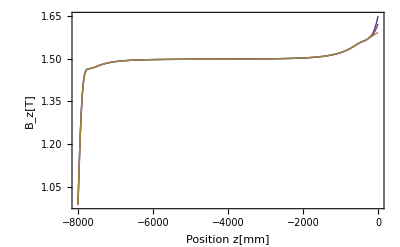

```mathematica
Plot[{B8z[{0,30.,z}],B8z[{0,0,z}],B8z[{0,-30,z}]},{z,-8000,0},PlotRange->{All,All},PlotStyle->Thick,FrameLabel->{" Position z[mm]","B_z[T]"},LabelStyle->{18},LabelStyle->{18},Frame->True,Axes->False,PlotLegend->{"x = 0 mm, y = +30 mm","x = 0 mm, y =   0 mm","x = 0 mm, y = -30 mm"},LegendPosition->{-0.5,0},LegendSize->0.6,ShadowBackground->White,LegendTextSpace->5]
```

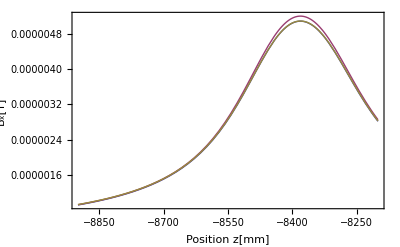

```mathematica
Plot[{B8x[{0,30.,z}],B8x[{0,0,z}],B8x[{0,-30,z}]},{z,-8000,0},PlotRange->{All,All},PlotStyle->Thick,FrameLabel->{" Position z[mm]","B_x[T]"},LabelStyle->{18},LabelStyle->{18},Frame->True,Axes->False,PlotLegend->{"x = 0 mm, y = +30 mm","x = 0 mm, y =   0 mm","x = 0 mm, y = -30 mm"},LegendPosition->{-0.5,0},LegendSize->0.6,ShadowBackground->White,LegendTextSpace->5]
```

```mathematica
Plot[{B8y[{0,30.,z}],B8y[{0,0,z}],B8y[{0,-30.,z}]},{z,-8900,-8200},PlotRange->{All,All},PlotStyle->Thick,FrameLabel->{" Position z[mm]","B_y[T]"},LabelStyle->{18},LabelStyle->{18},Frame->True,Axes->False,PlotLegend->{"x = 0 mm, y = +30 mm","x = 0 mm, y =   0 mm","x = 0 mm, y = -30 mm"},LegendPosition->{-0.55,0.24},LegendSize->0.6,ShadowBackground->White,LegendTextSpace->8]
```

```mathematica
Plot[{Norm[B8[{30,30,z}]],Norm[B8[{0,0,z}]],Norm[B8[{-30,-30,z}]]},{z,-8000,0},PlotRange->{All,All},PlotStyle->{Blue,Green,Red,Thickness[0.004]},FrameLabel->{" Position z[mm]","B[T]"},LabelStyle->{18},LabelStyle->{18},Frame->True,Axes->False,PlotLegend->{"obere Kante ","zentrale Achse ","untere Kante"},LegendPosition->{-0.4,0},LegendSize->0.5,ShadowBackground->White,LegendTextSpace->5]
```

### Comparison Radia - Magfield3

```mathematica
SetDirectory["C:\Users\carmen\Documents"];
Tabfield2=Import["field2.log","table"]; (*Magnetfeld Magfield 3 entlang zentraler Achse des langen Solenoiden*)
TabfieldRadia=Table[{z/1000,Norm[B8c[{0,0,z}]]}, {z,-8000,-10,1}]; (*Magnetfeld Radia entlang zentraler Achse des langen Solenoiden*)

Dimensions[Tabfield2[[1;;51,1]]]
Dimensions[TabfieldRadia[[All,1]]]
```

Comparison Radia - Magfield3

Part::take: Cannot take positions 1 through 51 in Tabfield.

{3}

{7991}

```mathematica
Magnetic Field along Fieldlines
```

```mathematica
SetDirectory["C:\Users\carmen\Documents"];
```

```mathematica
bf=Import["fieldlinemag.txt","table"];
```

```mathematica
ListPlot[{bf},Frame->True,Axes->False,FrameLabel->{"z ","B[T]"},LabelStyle->{18},Joined->True,PlotStyle->Thick]
```

```mathematica
TabGrp81=Table[{(t-4000)/1000,Norm[B8[Flatten[uu[t]/.fieldline1]]]}, {t,0,8000}];
TabGrp82=Table[{(t-4000)/1000,Norm[B8[Flatten[vv[t]/.fieldline2]]]}, {t,0,8000}];
TabGrp83=Table[{(t-4000)/1000,Norm[B8[Flatten[ww[t]/.fieldline3]]]}, {t,0,8000}];
```

```mathematica
TabGrp8c1=Table[{(t-4000)/1000.,Norm[B8c[Flatten[uuc[t]/.fieldline1c]]]}, {t,0,8000}];
TabGrp8c2=Table[{(t-4000)/1000.,Norm[B8c[Flatten[vvc[t]/.fieldline2c]]]}, {t,0,8000}];
TabGrp8c3=Table[{(t-4000)/1000.,Norm[B8c[Flatten[wwc[t]/.fieldline3c]]]}, {t,0,8000}];

TabGrp8c1//TableForm
TabGrp8c2//TableForm
TabGrp8c3//TableForm
Export["Bfieldl1_190115.txt",Flatten[TabGrp8c1,0],"Table"]
Export["Bfieldl2_190115.txt",Flatten[TabGrp8c2,0],"Table"]
Export["Bfield3_190115.txt",Flatten[TabGrp8c3,0],"Table"]
```

{{-4.,1.4991},{-3.999,1.4991},{-3.998,1.49911},{-3.997,1.49911},{-3.996,1.49911},{-3.995,1.49911},{-3.994,1.49911},{-3.993,1.49911},{-3.992,1.49911},{-3.991,1.49911},{-3.99,1.49912},{-3.989,1.49912},{-3.988,1.49912},{-3.987,1.49912},«7974»,{3.988,0.0370161},{3.989,0.0369393},{3.99,0.0368627},{3.991,0.0367864},{3.992,0.0367103},{3.993,0.0366344},{3.994,0.0365588},{3.995,0.0364834},{3.996,0.0364083},{3.997,0.0363334},{3.998,0.0362588},{3.999,0.0361843},{4.,0.0361101}}

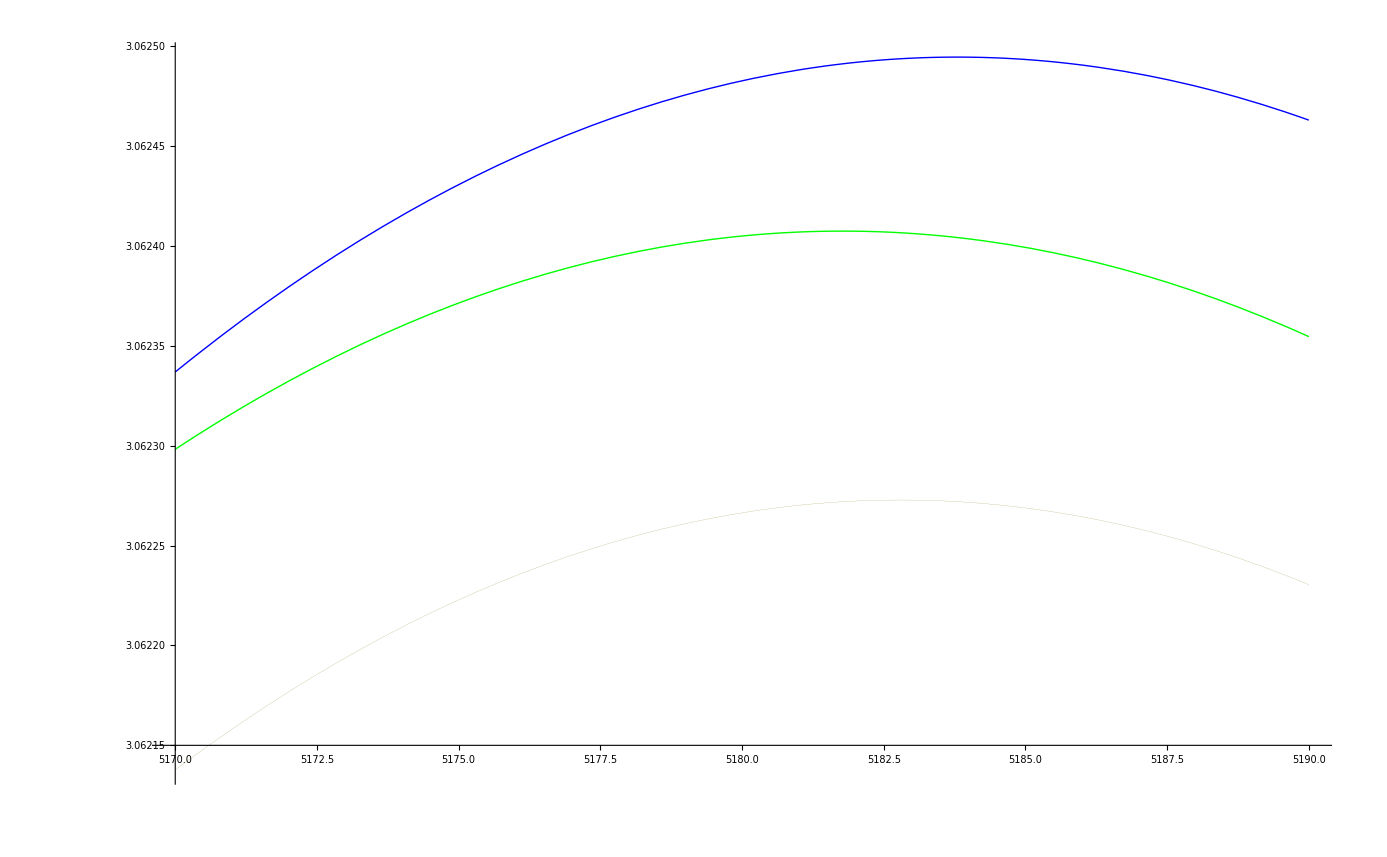

```mathematica
(*Magnetic field along fieldlines*)

Plot[{Norm[B8[Flatten[uu[t]/.fieldline1]]],Norm[B8[Flatten[vv[t]/.fieldline2]]],Norm[B8[Flatten[ww[t]/.fieldline3]]]},{t,5170,5190},PlotRange->{All,All},PlotStyle->{Green,Blue,Thickness[0.0001]},Frame->False, Axes->True,FrameLabel->{"Position z [mm]", " B [T]"},LabelStyle->{18},(*FrameTicks->{{{4500,500},{5500,1500},{6500,2500}},All},*)PlotStyle->Thick]
```

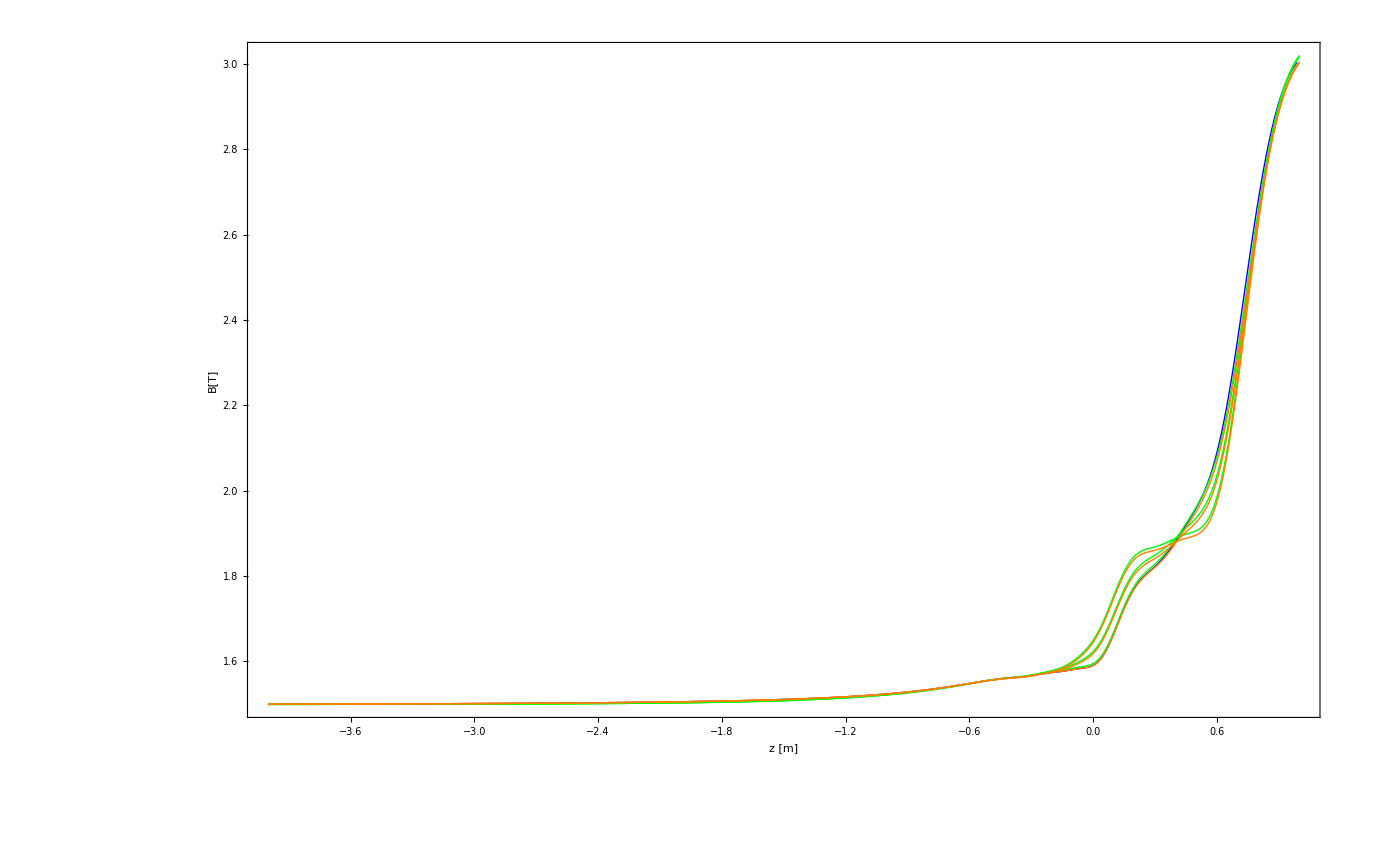

```mathematica
ListPlot[{bf[[1;;5000]],TabGrp81,TabGrp82,TabGrp83,TabGrp8c1,TabGrp8c2,TabGrp8c3},Frame->True,Axes->False,FrameLabel->{"z [m] ","B[T]"},LabelStyle->{18},Joined->True,PlotStyle->{Blue,Green,Green,Green,Orange,Orange,Orange}]
```

```mathematica
(*vector plot of magnetic field*)
RadPlot3DOptions[];
Show[VectorFieldPlot3D[B8[{x,y,z}],{x,0,0,0},{y,-30,30},{z,-8500,-7800},ScaleFactor->50,ScaleFunction->Normalize,VectorHeads->True],Axes->{False,True,True},AxesLabel->{"Position x[mm]", "Position y [mm]", "Position z [mm]"},LabelStyle->{18}]
```

Table::write: Tag Plus in -4000 + t is Protected.

General::stop: Further output of Table :: write will be suppressed during this calculation.

Show::gtype: ListVectorFieldPlot3D is not a type of graphics.

Show[ListVectorFieldPlot3D[Table[{N[{x,y,-4000+t}],N[B8[{x,y,z}]]},{x,0,0,0},{y,-30,30,10},{-4000+t,-8500,-7800,350/3}],{ScaleFactor→50,ScaleFunction→Normalize,VectorHeads→True,ScaleFactor→50}],Axes→{False,True,True},AxesLabel→{Position x[mm],Position y [mm],Position z [mm]},LabelStyle→{18}]

## Fieldlines

```mathematica
fieldline1=NDSolve[{uu'[t]==B8[uu[t]]/Norm[B8[uu[t]]],uu[0]=={0,30,-4000}},{uu},{t,0,10000},Method->"BDF" ];
```

```mathematica
fieldline2=NDSolve[{vv'[t]==B8[vv[t]]/Norm[B8[vv[t]]],vv[0]=={0,-30,-4000}},{vv},{t,0,10000},Method->"BDF"];
```

```mathematica
fieldline3=NDSolve[{ww'[t]==B8[ww[t]]/Norm[B8[ww[t]]],ww[0]=={0,0,-4000}},{ww},{t,0,10000},Method->"BDF"];
```

```mathematica
fieldline4=NDSolve[{sss'[t]==B8[sss[t]]/Norm[B8[sss[t]]],sss[0]=={30,30,-4000}},{sss},{t,0,10000},Method->"BDF"];
```

```mathematica
fieldline5=NDSolve[{ttt'[t]==B8[ttt[t]]/Norm[B8[ttt[t]]],ttt[0]=={0,0,-4000}},{ttt},{t,0,10000},Method->"BDF"];
```

```mathematica
fieldline1c=NDSolve[{uuc'[t]==B8c[uuc[t]]/Norm[B8c[uuc[t]]],uuc[0]=={0,30,-4000}},{uuc},{t,0,10000},Method->"BDF" ];
```

```mathematica
fieldline2c=NDSolve[{vvc'[t]==B8c[vvc[t]]/Norm[B8c[vvc[t]]],vvc[0]=={0,-30,-4000}},{vvc},{t,0,10000},Method->"BDF" ];
```

NDSolve::nlnum: The function value {82.4803\ Null} is not a list of numbers with dimensions {3} at {t, vvc[t]} = {8099.93, {-0.0000398185, -207.9, 4058.79}}.

```mathematica
fieldline3c=NDSolve[{wwc'[t]==B8c[wwc[t]]/Norm[B8c[wwc[t]]],wwc[0]=={0,0,-4000}},{wwc},{t,0,10000},Method->"BDF" ];
```

```mathematica
Magnetic Field Homogeneity
```

```mathematica
TabHomB1=Table[{(t-4000)/1000,(Norm[B8[Flatten[uu[t]/.fieldline1]]]-Norm[B8[Flatten[ww[t]/.fieldline3]]])/Norm[B8[Flatten[ww[t]/.fieldline3]]]}, {t,5182,5186}];
```

```mathematica
TabHomB2=Table[{(t-4000)/1000,(Norm[B8[Flatten[sss[t]/.fieldline4]]]-Norm[B8[Flatten[ww[t]/.fieldline3]]])/Norm[B8[Flatten[ww[t]/.fieldline3]]]}, {t,5182,5186}];
```

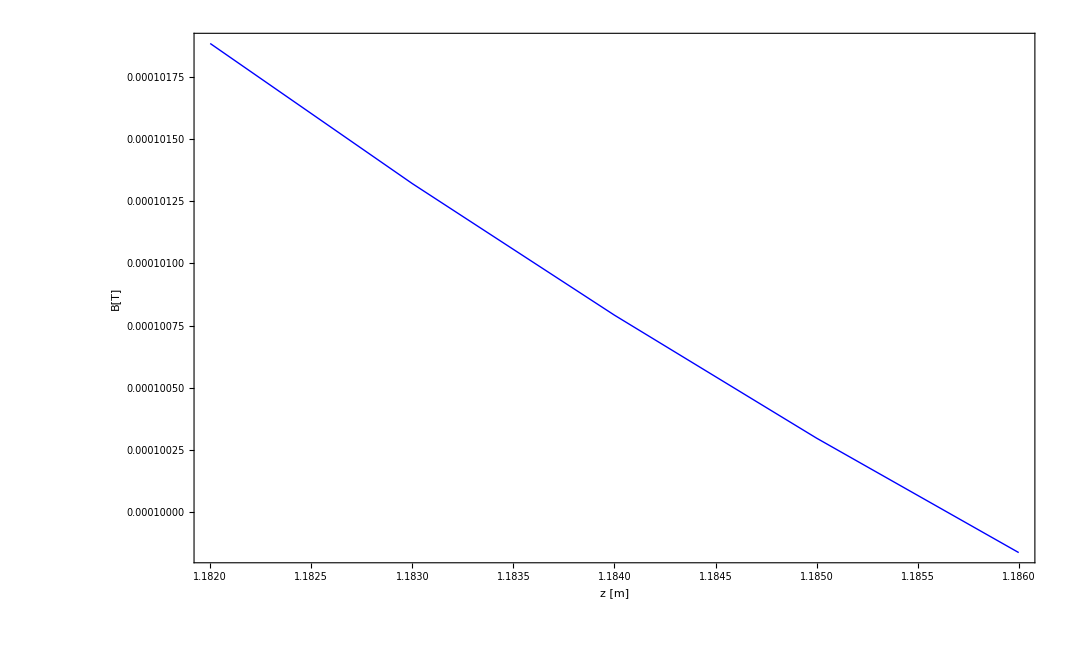

```mathematica
ListPlot[{TabHomB2},Frame->True,Axes->False,FrameLabel->{"z [m] ","B[T]"},LabelStyle->{18},Joined->True,PlotStyle->{Blue}]
```

## Geometry backscatterdetector

```mathematica
drw8=radObjDrw[Grp8];

Bore=radObjRaceTrk[{0,0,-7500},{150,152},{0,0},6000,12,124.22,"auto","z"];
radObjDrwAtr[Bore,{0,0.2,0},thcn];

guide1=radObjRaceTrk[{0,0,-7500},{0.1,0.2},{60,60},800,12,124.22,"auto","z"];
guide2=radObjRaceTrk[{0,0,-7500},{0.1,0.2},{100,100},800,12,124.22,"auto","z"];
guide3=radObjRaceTrk[{0,0,-8600},{0.1,0.2},{50,50},200,12,124.22,"auto","z"];
guide4=radObjRaceTrk[{0,0,-8600},{0.1,0.2},{90,90},200,12,124.22,"auto","z"];
radObjDrwAtr[guide1,{0,0.2,1},thcn];
radObjDrwAtr[guide2,{0,0.2,0.5},thcn];
radObjDrwAtr[guide3,{0,0.2,1},thcn];
radObjDrwAtr[guide4,{0,0.2,0.5},thcn];
radObjDrw[radObjCnt[{framebar,Rt1,Bore}]];

bar1= radObjRecMag[{785,0,-8380},{1290,140,140},{0,0,0}];
radObjDrwAtr[bar1,{0,1,1},thcn];

bar2= radObjRecMag[{-785,0,-8380},{1290,140,140},{0,0,0}];
radObjDrwAtr[bar2,{0,1,1},thcn];

shield1a= radObjRecMag[{90.47,0,-8111},{77.74,140,100},{0,0,0}];
radObjDrwAtr[shield1a,{0,1,1},thcn];

shield1b= radObjThckPgn[0,140,{{-8161,51.6},{-8061,51.6},{-8061,38.2}},"y"];
radObjDrwAtr[shield1b,{0,1,1},thcn];

shield2a= radObjRecMag[{-90.47,0,-8111},{77.74,140,100},{0,0,0}];
radObjDrwAtr[shield2a,{0,1,1},thcn];

shield2b= radObjThckPgn[0,140,{{-8161,-51.6},{-8061,-51.6},{-8061,-38.2}},"y"];
radObjDrwAtr[shield2b,{0,1,1},thcn];

shield3a= radObjRecMag[{0,60.8,-8111},{76.4,18.4,100},{0,0,0}];
radObjDrwAtr[shield3a,{0,1,1},thcn];

shield3b= radObjThckPgn[0,76.4,{{38.2,-8061},{51.6,-8061},{51.6,-8161}},"x"];
radObjDrwAtr[shield3b,{0,1,1},thcn];

shield3c=radObjPolyhdr[{{38.2,70,-8061},{51.6,70,-8161},{38.2,70,-8161},{38.2,51.6,-8161},{51.6,51.6,-8161},{38.2,38.2,-8061}},{{1,2,3},{2,3,4,5},{4,5,6},{1,3,4,6},{1,2,5,6}},{0,0,0}];
radObjDrwAtr[shield3c,{0,1,1},thcn];

shield3d=radObjPolyhdr[{{-38.2,70,-8061},{-51.6,70,-8161},{-38.2,70,-8161},{-38.2,51.6,-8161},{-51.6,51.6,-8161},{-38.2,38.2,-8061}},{{1,2,3},{2,3,4,5},{4,5,6},{1,3,4,6},{1,2,5,6}},{0,0,0}];
radObjDrwAtr[shield3d,{0,1,1},thcn];



shield4a= radObjRecMag[{0,-60.8,-8111},{76.4,18.4,100},{0,0,0}];
radObjDrwAtr[shield4a,{0,1,1},thcn];

shield4b= radObjThckPgn[0,76.4,{{-38.2,-8061},{-51.6,-8061},{-51.6,-8161}},"x"];
radObjDrwAtr[shield4b,{0,1,1},thcn];

shield4c=radObjPolyhdr[{{38.2,-70,-8061},{51.6,-70,-8161},{38.2,-70,-8161},{38.2,-51.6,-8161},{51.6,-51.6,-8161},{38.2,-38.2,-8061}},{{1,2,3},{2,3,4,5},{4,5,6},{1,3,4,6},{1,2,5,6}},{0,0,0}];
radObjDrwAtr[shield4c,{0,1,1},thcn];

shield4d=radObjPolyhdr[{{-38.2,-70,-8061},{-51.6,-70,-8161},{-38.2,-70,-8161},{-38.2,-51.6,-8161},{-51.6,-51.6,-8161},{-38.2,-38.2,-8061}},{{1,2,3},{2,3,4,5},{4,5,6},{1,3,4,6},{1,2,5,6}},{0,0,0}];
radObjDrwAtr[shield4d,{0,1,1},thcn];

shield1plate= radObjRecMag[{0,75,-8111},{258.68,10,100},{0,0,0}];
radObjDrwAtr[shield1plate,{0,1,1},thcn];

shield2plate= radObjRecMag[{0,75,-8480},{258.68,10,50},{0,0,0}];
radObjDrwAtr[shield2plate,{0,1,1},thcn];


det1= radObjThckPgn[0,140,{{-8450,-60},{-8450,-140},{-8310,-140}},"y"];
radObjDrwAtr[det1,{0,1,1},thcn];

det2 = radObjThckPgn[0,140,{{-8450,60},{-8450,140},{-8310,140}},"y"];
radObjDrwAtr[det2,{0,1,1},thcn];

det3=radObjRecMag[{-87,0,-8389},{5,140,142.69},{0,0,0}];
radObjDrwAtr[det3,{0,1,1},thcn];
radTrfOrnt[det3,radTrfRot[{-82,0,-8389},{0,-1,0},31.26 Degree]];

det4=radObjRecMag[{87,0,-8389},{5,140,142.69},{0,0,0}];
radObjDrwAtr[det4,{0,1,1},thcn];
radTrfOrnt[det4,radTrfRot[{82,0,-8389},{0,-1,0},-31.26 Degree]];

shield5a= radObjRecMag[{84.36,0,-8480},{89.96,140,50},{0,0,0}];
radObjDrwAtr[shield5a,{0,1,1},thcn];

shield5b= radObjThckPgn[0,140,{{-8505,39.38},{-8455,39.38},{-8455,29.34}},"y"];
radObjDrwAtr[shield5b,{0,1,1},thcn];

shield6a= radObjRecMag[{-84.36,0,-8480},{89.96,140,50},{0,0,0}];
radObjDrwAtr[shield6a,{0,1,1},thcn];

shield6b= radObjThckPgn[0,140,{{-8505,-39.38},{-8455,-39.38},{-8455,-29.34}},"y"];
radObjDrwAtr[shield6b,{0,1,1},thcn];

shield7a= radObjRecMag[{0,54.1,-8480},{58.66,31.8,50},{0,0,0}];
radObjDrwAtr[shield7a,{0,1,1},thcn];

shield7b= radObjThckPgn[0,58.66,{{29.34,-8455},{39.38,-8455},{39.38,-8505}},"x"];
radObjDrwAtr[shield7b,{0,1,1},thcn];

shield7c=radObjPolyhdr[{{29.34,70,-8455},{39.38,70,-8505},{29.34,70,-8505},{29.34,38.2,-8505},{39.38,38.2,-8505},{29.34,29.34,-8455}},{{1,2,3},{2,3,4,5},{4,5,6},{1,3,4,6},{1,2,5,6}},{0,0,0}];
radObjDrwAtr[shield7c,{0,1,1},thcn];

shield7d=radObjPolyhdr[{{-29.34,70,-8455},{-39.38,70,-8505},{-29.34,70,-8505},{-29.34,38.2,-8505},{-39.38,38.2,-8505},{-29.34,29.34,-8455}},{{1,2,3},{2,3,4,5},{4,5,6},{1,3,4,6},{1,2,5,6}},{0,0,0}];
radObjDrwAtr[shield7d,{0,1,1},thcn];



shield8a= radObjRecMag[{0,-54.1,-8480},{58.66,31.8,50},{0,0,0}];
radObjDrwAtr[shield8a,{0,1,1},thcn];

shield8b= radObjThckPgn[0,58.66,{{-29.34,-8455},{-39.38,-8455},{-39.38,-8505}},"x"];
radObjDrwAtr[shield8b,{0,1,1},thcn];

shield8c=radObjPolyhdr[{{29.34,-70,-8455},{39.38,-70,-8505},{29.34,-70,-8505},{29.34,-38.2,-8505},{39.38,-38.2,-8505},{29.34,-29.34,-8455}},{{1,2,3},{2,3,4,5},{4,5,6},{1,3,4,6},{1,2,5,6}},{0,0,0}];
radObjDrwAtr[shield8c,{0,1,1},thcn];

shield8d=radObjPolyhdr[{{-29.34,-70,-8455},{-39.38,-70,-8505},{-29.34,-70,-8505},{-29.34,-38.2,-8505},{-39.38,-38.2,-8505},{-29.34,-29.34,-8455}},{{1,2,3},{2,3,4,5},{4,5,6},{1,3,4,6},{1,2,5,6}},{0,0,0}];
radObjDrwAtr[shield8d,{0,1,1},thcn];
```

```mathematica
RadPlot3DOptions[];
Show[Graphics3D[{Opacity[1],radObjDrw[radObjCnt[{Rt1,det1,det2,guide1,guide3,bar1,bar2,det3,det4,(*,shield1plate,shield2plate,shield1a,shield1b,shield2a,shield2b,shield3a,shield3b,shield3c,shield3d,shield4a,shield4b,shield4c,shield4d,shield5a,shield5b,shield6a,shield6b,shield7a,shield7b,shield7c,shield7d,shield8a,shield8b,shield8c,shield8d,*)guide2,guide4}]]},PlotRange->{{-300,300},{-300,300},{-8700,-7800}}],Graphics3D[{Opacity[0.2],radObjDrw[radObjCnt[{Bore}]]},BaseStyle->Large,PlotRange->{{-300,300},{-300,300},{-8700,-7800}},Boxed->True],
(*VectorFieldPlot3D[{80,0,140},{x,46,46},{y,0,0},{z,-8450,-8450},ScaleFactor->1000,ScaleFunction->Normalize,VectorHeads->False],*)
(*VectorFieldPlot3D[{-63,0,1472},{x,33,33},{y,0,0},{z,-8472,-8472},ScaleFactor->1200,ScaleFunction->Normalize,VectorHeads->False]*)
(*ParametricPlot3D[{Evaluate[uu[t]/.fieldline45a]},{t,0,465},PlotStyle->Directive[Red,Thick]] ,
ParametricPlot3D[{Evaluate[vv[t]/.fieldline46]},{t,0,465},PlotStyle->Directive[Red,Thick]],
ParametricPlot3D[{Evaluate[ww[t]/.fieldline47]},{t,0,480},PlotStyle->Directive[Red,Thick]],
ParametricPlot3D[{Evaluate[bbbb [t]/.fieldline77]},{t,0,700},PlotStyle->Directive[Red,Thick]]*),Axes-> {True,False,True},AxesLabel->{ "Position x [mm]","Position y [mm]", "Position z [mm]"},LabelStyle->{20},TicksStyle->Directive[Black,20](*,Ticks->{{{300,-30},{0,0},{-300,30}},{},{{-8000,0},{-8310,31},{-8450,45}}}*)]
```

-Graphics3D-

## Adiabaticity

```mathematica
v0=800*1000 (*mm/s*);
T[{x_,y_,z_}]:= 2*Pi/1.832/10^8/Norm[B8[{x,y,z}]];
```

```mathematica
adiabaticity11[{x_,y_,z_}]:=ArcCos[(B8[{x,y,z+v0*T[{x,y,z}]}]).(B8[{x,y,z}])/(Norm[B8[{x,y,z+v0*T[{x,y,z}]}]])/(Norm[B8[{x,y,z}]])]/2/Pi
```

```mathematica
ad1=Table[{z,adiabaticity11[{0,30,z}]},{z,-8700,-8200,1}]
```

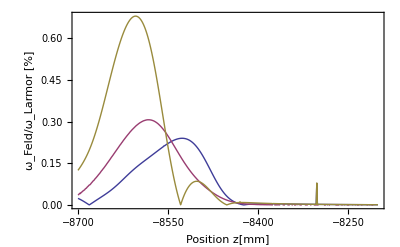

```mathematica
ListPlot[{Transpose[{ad1[[All,1]],ad1[[All,2]]*100}],Transpose[{ad2[[All,1]],ad2[[All,2]]*100}],Transpose[{ad3[[All,1]],ad3[[All,2]]*100}]},Joined->True,PlotStyle->Thick,FrameLabel->{" Position z[mm]","ω_Feld/ω_Larmor [%]"},LabelStyle->{18},Frame->True,Axes->True,PlotLegend->{"x= 0 mm, y= +30 mm","x= 0 mm, y=     0 mm","x= 0 mm, y= -30 mm"},LegendPosition->{0.,0.1},LegendSize->0.7,ShadowBackground->White,LegendTextSpace->5,PlotRange->All]
```

## Forces

```mathematica
radFldEnrFrc[Rt1,GrpFrc1,"fx"]
radFldEnrFrc[Rt1,GrpFrc1,"fy"]
radFldEnrFrc[Rt1,GrpFrc1,"fz"]
```

{0.000722789,0.00114016,20003.4}

```mathematica
{{GrpFrc1=radObjCnt[{Rt4,Rt5,Rt6,Rt7,Rt8,Rt9,Rt10,Rt11,Rt12,Rt13,framebar,platesh,platesv}];
GrpFrc4=radObjCnt[{Rt1,Rt2,Rt3,Rt5,Rt6,Rt7,Rt8,Rt9,Rt10,Rt11,Rt12,Rt13,framebar,platesh,platesv}];
GrpFrc5=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt6,Rt7,Rt8,Rt9,Rt10,Rt11,Rt12,Rt13,framebar,platesh,platesv}];
GrpFrc6=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5,Rt7,Rt8,Rt9,Rt10,Rt11,Rt12,Rt13,framebar,platesh,platesv}];}, {GrpFrc7=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5,Rt6,Rt8,Rt9,Rt10,Rt11,Rt12,Rt13,framebar,platesh,platesv}];
GrpFrc8=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5,Rt6,Rt7,Rt9,Rt10,Rt11,Rt12,Rt13,framebar,platesh,platesv}];}, {GrpFrc9=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5,Rt6,Rt7,Rt8,Rt10,Rt11,Rt12,Rt13,framebar,platesh,platesv}];
GrpFrc10=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5,Rt6,Rt7,Rt8,Rt9,Rt11,Rt12,Rt13,framebar,platesh,platesv}];
GrpFrc11=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5,Rt6,Rt7,Rt8,Rt9,Rt10,Rt12,Rt13,framebar,platesh,platesv}];
GrpFrc12=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5,Rt6,Rt7,Rt8,Rt9,Rt10,Rt11,Rt13,framebar,platesh,platesv}];
GrpFrc13=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5,Rt6,Rt7,Rt8,Rt9,Rt10,Rt11,Rt12,framebar,platesh,platesv}];}}
```

```mathematica
?radObjDrwAtr
```

radObjDrwAtr[obj,{r,g,b},thcn] applies RGB color {r,g,b} and line thickness thcn to object obj.